# Aggregate all cMUP data (ValScan, GlyScan, SlowChip)

```mathematica
notebookVersion=2.0;

keysUsed={"MutantID","ExpIndex","ManualGFPFlag","UniqueExptID","ChipType","LocalBackgroundRatio","Indices","EnzymeConc","fit_mm_datapoints","DataPointsOptLinFit","fit_mm_curved_r2","fit_mm_kcat","fit_mm_KM","fit_mm_scale_factor","FitR2","DataPoints","kcat","Km","ScaleFactor","SubstrateConc","OptLinFitSlope","kcat/Km","AllLBRs","AllInitialRates","AllSubstrateConcs","StdCurveR2","NumPointsLinearFits","fit_mm_kcat_param_error","fit_mm_KM_param_error","AllEnzymeConcs"};

(* modified median function to return value if length of list = 1 *)
median2[x_]:=If[Length[x]==0,Median[{x}],Median[x]]

(*expIndexToCullOn=7;*)

SconcToCullOn=50.0;

twoPointCutoff=6;

rSqaredCutoff=0.97;

calcRatio[indices_,Sconc_]:=Module[{repeatRate,initRate},

initRate=allGrouped[indices][Select[#AssayType==1&&#SubstrateConc==Sconc&]][1,"OptLinFitSlope"];

repeatRate=allGrouped[indices][Select[#AssayType==0&]][1,"OptLinFitSlope"];

repeatRate/initRate]

generateDatasetFromCSV[in_,type_,id_,keysToTake_:keysUsed]:=Module[{dsIn,keys},

dsIn=in;

keys=dsIn[[1]];

r2key=Select[keysToTake,StringContainsQ[#,"curved_r2"]&][[1]];
dataPointsKey=Select[keysToTake,StringContainsQ[#,"datapoints"]&][[1]];

kcatKey=Select[keysToTake,StringContainsQ[#,"_kcat"]&][[1]];
KmKey=Select[keysToTake,StringContainsQ[#,"_KM"]&][[1]];
kcatUncorrected=kcatKey;
scaleFactorKey=Select[keysToTake,StringContainsQ[#,"scale_factor"]&][[1]];

all=Dataset[Table[Append[Association[Table[{keys[[n]]->dsIn[[i+1,n]]},{n,1,Length[keys]}]],{"ChipType"->type,"UniqueExptID"->id}],{i,1,Length[dsIn]-1}]];

repeatSconc=allGrouped[1][Select[#AssayType==0&]][1,"SubstrateConc"];

allGrouped=all[GroupBy["Indices"]];

all2=all[All,Append[#,{"FitR2"->#[r2key],"DataPoints"->#[dataPointsKey],"kcat"->#[kcatKey],"Km"->#[KmKey],"kcat/Km"->#[kcatKey]/(#[KmKey]*10^-6),"ScaleFactor"->#[scaleFactorKey],"AllLBRs"->Normal[allGrouped[#Indices][All,"LocalBackgroundRatio"]],"AllInitialRates"->Normal[allGrouped[#Indices][All,"OptLinFitSlope"]],"AllSubstrateConcs"->Normal[allGrouped[#Indices][All,"SubstrateConc"]],"AllEnzymeConcs"->Normal[allGrouped[#Indices][All,"EnzymeConc"]],"StdCurveR2"->(LinearModelFit[Normal[allGrouped[#Indices][1,"StdCurveData"]]]["RSquared"]),"NumPointsLinearFits"->(Length[ToExpression[#]]&/@Normal[allGrouped[#Indices][All,"DataPointsOptLinFit"]]),"Num2ptFits"->Count[(Length[ToExpression[#]]&/@Normal[allGrouped[#Indices][All,"DataPointsOptLinFit"]]),2]}]&];

all2[All,keysToTake]

]

(* function for remapping mutants with eGFP mutations and biomek errors *)

remapNames[dataset_]:=Module[{replaced1,replaced2,newDs},

remappingRules={"P76G"->"P92G","H172G"->"I188G*","T268G"->"D284G","A364G"->"M380G","N460G"->"L476G","T84V"->"D101V","T189V"->"N206V","G289V"->"G308V","I393V"->"D411V","P497V"->"P513V","H486E"->"H353E"};

addFlags={"P448V"->"P448V*","Q131V"->"Q131V*","T425G"->"T425G*","N205G"->"N205G*","Y192G"->"Y192G*","G289V"->"G289V*","I188G"->"I188G*"};

dsToAssociation=Normal[dataset];

replaced1=Fold[Replace[#1,#2,Infinity]&,dsToAssociation,remappingRules];

replaced2=Fold[Replace[#1,#2,Infinity]&,replaced1,addFlags];

newDs=Dataset[replaced2];

newDs[All,Append[#,"KnownBadMutant"->If[MemberQ[addFlags[[All,2]],#MutantID],1,0]]&]

]

(* removed R2 flags *)

cullBadChambers[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

grouped=dataset[GroupBy["Indices"]];

countFitPoints=Table[{ToExpression[grouped[n,1,"Indices"]],Length[ToExpression[#]]&/@Normal[grouped[n,All,"DataPointsOptLinFit"]]},{n,1,Length[grouped]}];

twoPointFits=Select[countFitPoints,Count[#[[2]],2]≥twoPointCutoff&][[All,1]];

Print[twoPointFits];

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

dataset[Select[(#SubstrateConc==SconcToCullOn||#SubstrateConc==Round[SconcToCullOn])&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>5.0&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&&#["kcat/Km"]>0&&#["kcat"]>0&]]

]

cullExpressors[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

grouped=dataset[GroupBy["Indices"]];

countFitPoints=Table[{ToExpression[grouped[n,1,"Indices"]],Length[ToExpression[#]]&/@Normal[grouped[n,All,"DataPointsOptLinFit"]]},{n,1,Length[grouped]}];

twoPointFits=Select[countFitPoints,Count[#[[2]],2]≥2&][[All,1]];

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

(*dataset[Select[(#SubstrateConc==SconcToCullOn||#SubstrateConc==Round[SconcToCullOn])&&(#LocalBackgroundRatio≤5.0||#["FitR2"]≤0.97)&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]]*)

(* removed fitR2 flag *)
dataset[Select[(#SubstrateConc==SconcToCullOn||#SubstrateConc==Round[SconcToCullOn])&&(#LocalBackgroundRatio≤5.0||#["kcat/Km"]≤0||#["kcat"]≤0)&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]]

]
```

#### Import all Michaelis-Menten data (1 csv per experiment):

For each individual experiment, the CSV file is imported and then the following functions are applied sequentially:

1. 'generateDatasetFromCSV' - converts CSV "Table" format into Dataset format. I'm also appending the chip type (e.g. GlyScan) and the filename in order to ensure that each experiment contains a unique identifier string.

2. 'cullBadChambers' - this function groups the data by chamber and applies our standard QC criteria as selection criteria, removing those chambers that are bad/low-quality.

```mathematica
files={{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190314_S3_d1_MeP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190318_S3_d1_MeP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190321_S2_d2_MeP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190117_S3_d1_MeP_1_GlyScan.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190123_S3_d1_MeP_1_GlyScan.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190522_S2_d1_MeP_1_SlowChip.csv.bz2","SlowChip"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190605_S2_d1_MeP_1_SlowChip.csv.bz2","SlowChip"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190913_S2_d1_MeP_1_SlowMeP.csv.bz2","SlowMePChip"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190913_S3_d1_MeP_1_SlowMeP.csv.bz2","SlowMePChip"}
};

inputFilePaths=files[[All,1]]

scanType=files[[All,2]]
```

{/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190314_S3_d1_MeP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190318_S3_d1_MeP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190321_S2_d2_MeP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190117_S3_d1_MeP_1_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190123_S3_d1_MeP_1_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190522_S2_d1_MeP_1_SlowChip.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190605_S2_d1_MeP_1_SlowChip.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190913_S2_d1_MeP_1_SlowMeP.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MeP/190913_S3_d1_MeP_1_SlowMeP.csv.bz2}

{ValScan,ValScan,ValScan,GlyScan,GlyScan,SlowChip,SlowChip,SlowMePChip,SlowMePChip}

Note: Need the append below for a single SlowChip experiment for which I need to change some keys:

```mathematica
ProgressIndicator[Dynamic[itr],{1,Length[inputFilePaths]}]

pathLengthToDrop={53,53,53,53,53,53,53,53,53};

datasets=Join[Table[remapNames[generateDatasetFromCSV[Import[inputFilePaths[[itr]],"Data"],scanType[[itr]],StringDrop[StringDrop[inputFilePaths[[itr]],-4],pathLengthToDrop[[itr]]]]],{itr,1,Length[inputFilePaths]}]];

culledWithLigands=Join@@Table[cullBadChambers[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

culledIn=culledWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

{}

{}

{{28,19},{28,18},{28,22},{28,10},{13,56},{19,56},{19,54},{1,30},{16,30},{2,33},{1,54},{1,51}}

{}

{}

{{15,32},{22,50},{15,36},{16,45},{17,50},{19,20},{19,21},{23,52},{26,8},{23,10},{14,44},{15,52},{13,21},{14,19},{15,48},{26,34},{10,34},{9,29},{9,41},{11,20},{13,39},{12,19},{9,53},{5,44},{8,51},{10,51},{10,15},{6,12},{16,51},{12,53},{2,20},{2,44},{20,19},{2,36},{5,10},{2,11}}

{{26,8},{14,19},{26,18},{11,20},{14,44},{22,50},{6,21},{13,39},{9,41},{23,52},{15,53},{26,34},{16,51},{1,36},{1,37},{1,50},{1,39},{1,42},{1,51},{1,41},{1,45},{1,56},{1,54},{1,43},{1,55},{1,40},{1,49},{1,46},{1,47},{1,44},{1,53},{1,52},{1,38}}

{{28,19},{28,25},{10,8},{2,15},{24,10},{10,11},{9,16},{2,45},{2,8},{27,12},{3,8},{28,35},{6,13},{6,11},{3,4},{2,43},{4,29},{23,20},{25,11},{7,16},{4,27},{4,47},{27,16},{22,24},{25,28},{24,11},{16,18},{21,13},{3,48},{3,5},{10,7},{1,20},{3,7},{8,3},{22,4},{1,15},{8,27},{13,32},{11,51},{23,4},{14,8},{14,10},{1,5},{14,4},{21,28},{14,6},{14,5},{14,3},{14,7},{14,56},{14,55},{14,9}}

{{28,19},{28,25},{10,56},{1,20},{27,35},{2,55},{1,15},{1,24},{21,26},{25,51},{16,28},{15,20},{11,51},{16,18},{2,45},{2,43},{24,44},{23,48},{8,27},{6,13},{4,29},{1,23},{1,5},{1,3}}

```mathematica
slowWithLigands=Join@@Table[cullExpressors[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

slowIn=slowWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

```mathematica
unmeasuredIn=Complement[Normal[DeleteDuplicates[slowIn[All,"MutantID"]]],Normal[DeleteDuplicates[culledIn[All,"MutantID"]]]];
```

Group the aggregate dataset by mutant and print out a list of the experimental ID strings (for fast chips only):

```mathematica
groupedbyMutantInFastChips=culledIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&&#ChipType≠"SlowMePChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2FastChips=KeySortBy[groupedbyMutantInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInFastChips=slowIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&&#ChipType≠"SlowMePChip"&]][GroupBy["MutantID"]];

tooSlowIn2FastChips=KeySortBy[tooSlowInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

(* SlowChip *)

groupedbyMutantInSlowChip=culledIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowChip=KeySortBy[groupedbyMutantInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowChip=slowIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowChip=KeySortBy[tooSlowInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]

(* SlowMePChip *)

groupedbyMutantInSlowestChip=culledIn[Select[#ChipType=="SlowMePChip"||#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowestChip=KeySortBy[groupedbyMutantInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowestChip=slowIn[Select[#ChipType=="SlowMePChip"||#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowestChip=KeySortBy[tooSlowInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]
```

Dataset[<>]

Dataset[<>]

Perform additional culling step on mutants for which only 1-2 of many replicates passed culling.

Using a higher threshold for the SlowestChip data, as this has skipped chambers and the background dynamic range is much lower.

```mathematica
Dynamic[mutant]

cutoffThreshold=0.6;

(* SlowMeP devices - not skipping chambers so using 0.6 as the cutoff threshold *)
cutoffThresholdSlowest=0.6;

cullTableFast=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2FastChips[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2FastChips[mutant,1,"MutantID"],fractionCulled,"FastChip",(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2FastChips]}];

cullTableSlow=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],fractionCulled,"SlowChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowChip]}];

cullTableSlowest=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowestChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],fractionCulled,"SlowMePChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowestChip]}];

passedCullingFast=Select[cullTableFast,#[[2]]>cutoffThreshold&]
passedCullingSlow=Select[cullTableSlow,#[[2]]>cutoffThreshold&]
passedCullingSlowest=Select[cullTableSlowest,#[[2]]>cutoffThresholdSlowest&]
```

{{V26G,0.75,FastChip,4},{G34V,0.888889,FastChip,9},{Y48V,0.625,FastChip,8},{S50G,0.666667,FastChip,3},{K51G,0.75,FastChip,4},{G53A,0.75,FastChip,4},{R59V,0.833333,FastChip,6},{N69V,0.666667,FastChip,3},{D73V,0.9,FastChip,10},{V75A,0.75,FastChip,4},{T79S,0.615385,FastChip,91},{A80V,0.8,FastChip,5},{H83G,0.75,FastChip,4},{S85V,0.666667,FastChip,6},{V91A,0.666667,FastChip,3},{V91G,0.75,FastChip,4},{G130V,0.8,FastChip,5},{H132V,0.8,FastChip,5},{W138G,0.75,FastChip,4},{V142G,0.75,FastChip,4},{V159A,0.666667,FastChip,3},{P174V,0.75,FastChip,4},{G176A,0.75,FastChip,4},{D203G,0.666667,FastChip,3},{F204V,0.75,FastChip,4},{T228G,0.75,FastChip,4},{S230G,0.75,FastChip,4},{D233G,0.75,FastChip,4},{W237V,0.666667,FastChip,6},{P250G,0.666667,FastChip,3},{I265G,0.75,FastChip,4},{R266G,0.75,FastChip,4},{L274G,0.75,FastChip,4},{T304G,0.75,FastChip,4},{F333G,0.75,FastChip,4},{V347G,0.75,FastChip,4},{K366G,0.75,FastChip,4},{G370V,0.8,FastChip,5},{I394G,0.666667,FastChip,3},{N399V,0.666667,FastChip,6},{Y400G,0.666667,FastChip,3},{L427G,0.75,FastChip,4},{Y435V,0.666667,FastChip,6},{G458V,0.818182,FastChip,11},{S487G,0.666667,FastChip,3},{W489V,0.75,FastChip,4},{L498G,0.75,FastChip,4},{I505G,0.666667,FastChip,3},{S510V,0.833333,FastChip,6},{I519G,0.75,FastChip,4},{S525G,0.75,FastChip,4},{V536G,0.75,FastChip,4}}

{{Q39V,0.857143,SlowChip,7},{P92G,0.714286,SlowChip,7},{G99V,0.875,SlowChip,8},{N100V,0.666667,SlowChip,9},{T114G,0.625,SlowChip,8},{D116V,0.8,SlowChip,5},{S133V,0.8,SlowChip,5},{R164A,0.814815,SlowChip,27},{A165V,0.875,SlowChip,8},{W200G,0.833333,SlowChip,6},{W237V,0.714286,SlowChip,7},{H309V,0.875,SlowChip,8},{Y322G,0.666667,SlowChip,6},{D326V,0.8,SlowChip,5},{F333G,0.875,SlowChip,8},{Y345G,0.75,SlowChip,8},{G354V,0.9,SlowChip,10},{Y459G,0.75,SlowChip,8},{S464V,0.857143,SlowChip,7},{I496G,0.714286,SlowChip,7},{D518V,0.8,SlowChip,5},{S533V,0.625,SlowChip,8},{G537V,0.666667,SlowChip,6}}

{{N100A,0.736842,SlowMePChip,57},{R164A,0.947368,SlowMePChip,76},{W179V,0.666667,SlowMePChip,1}}

```mathematica
unmeasuredIn
unmeasuredFast=passedCullingFast[[All,1]]
unmeasuredSlow=passedCullingSlow[[All,1]]
unmeasuredSlowest=passedCullingSlowest[[All,1]]
```

{D116G,D144V,D305G,D305V,D326G,D352V,D38G,D38V,F178G,F332G,F500G,F57G,G171V,G465V,G502V,G56V,G64V,G82V,G89V,G96V,H353G,H486G,H486V,H495G,I167G,I447G,I97G,K162A,K162G,K162V,L297G,L31G,L329G,L336G,L35G,N100A/R164A,P92V,S160V,S190V,T79G,T79V,V523G,W102G,W179G,Y192V,Y193G}

{V26G,G34V,Y48V,S50G,K51G,G53A,R59V,N69V,D73V,V75A,T79S,A80V,H83G,S85V,V91A,V91G,G130V,H132V,W138G,V142G,V159A,P174V,G176A,D203G,F204V,T228G,S230G,D233G,W237V,P250G,I265G,R266G,L274G,T304G,F333G,V347G,K366G,G370V,I394G,N399V,Y400G,L427G,Y435V,G458V,S487G,W489V,L498G,I505G,S510V,I519G,S525G,V536G}

{Q39V,P92G,G99V,N100V,T114G,D116V,S133V,R164A,A165V,W200G,W237V,H309V,Y322G,D326V,F333G,Y345G,G354V,Y459G,S464V,I496G,D518V,S533V,G537V}

{N100A,R164A,W179V}

```mathematica
(* selecting chambers that have been identified as containing too many culled replicates, excepting those that have a second-order LBR >5 *)
slowPassedFastChip=culledIn[Select[MemberQ[passedCullingFast[[All,1]],#MutantID]&&(#ChipType=="GlyScan"||#ChipType=="ValScan")&]];
slowPassedSlowChip=culledIn[Select[MemberQ[passedCullingSlow[[All,1]],#MutantID]&&(#ChipType=="SlowChip")&]];
slowPassedSlowestChip=culledIn[Select[MemberQ[passedCullingSlowest[[All,1]],#MutantID]&&(#ChipType=="SlowMePChip"||#ChipType=="SlowestChip")&]];


culledFast=culledIn[Select[MemberQ[slowPassedFastChip,#]==False&]];

(* take Slow data that didn't meet criterion above - same as above except operating on culledFast *)
culledSlow=culledFast[Select[MemberQ[slowPassedSlowChip,#]==False&]];

(* take Slowest data that didn't meet criterion above - same as above except operating on culledSlow *)
culledSlowest=culledSlow[Select[MemberQ[slowPassedSlowestChip,#]==False&]]

slow=Join[slowPassedFastChip,slowPassedSlowChip,slowPassedSlowestChip,slowIn];

culled=culledSlowest;
```

Dataset[<>]

```mathematica
groupedbyMutantIn=culled[GroupBy["MutantID"]];

groupedbyMutant=KeySortBy[groupedbyMutantIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowIn=slow[GroupBy["MutantID"]];

tooSlow=KeySortBy[tooSlowIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

datasetsIn=DeleteDuplicates[Flatten[Values[Normal[groupedbyMutant[All,All,"UniqueExptID"]]]]]
```

{190117_S3_d1_MeP_1_GlyScan.csv,190123_S3_d1_MeP_1_GlyScan.csv,190314_S3_d1_MeP_1_ValScan.csv,190318_S3_d1_MeP_1_ValScan.csv,190321_S2_d2_MeP_1_ValScan.csv,190913_S2_d1_MeP_1_SlowMeP.csv,190913_S3_d1_MeP_1_SlowMeP.csv,190522_S2_d1_MeP_1_SlowChip.csv,190605_S2_d1_MeP_1_SlowChip.csv}

```mathematica
Print["Length of aggregate data set (number of unique measurements)"];
Length[culled]

mutantsWithData=Sort[DeleteDuplicates[Normal[culled[All,"MutantID"]]],ToExpression[StringDrop[StringDrop[#1,-1],1]]<ToExpression[StringDrop[StringDrop[#2,-1],1]]&];

Print["Number of total mutants with at least 1 Michaelis-Menten curve:"];
Length[mutantsWithData]

Print["Mutants too slow to have at least 1 culled measurement:"]
unmeasured=Complement[Normal[DeleteDuplicates[slow[All,"MutantID"]]],Normal[DeleteDuplicates[culled[All,"MutantID"]]]]

countRepsCulled=culled[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))&]][GroupBy["MutantID"]];

Print["Table of number of replicates per mutant:"]
Sort[Length[#]&/@countRepsCulled]

Print["Mean number of replicates per mutant:"]
N[Mean[Values[Normal[(Length[#]&/@countRepsCulled)]]]]
```

Length of aggregate data set (number of unique measurements)

5456

Number of total mutants with at least 1 Michaelis-Menten curve:

950

Mutants too slow to have at least 1 culled measurement:

{A165V,D116G,D116V,D144V,D203G,D305G,D305V,D326G,D326V,D352V,D38G,D38V,D518V,F178G,F204V,F332G,F333G,F500G,F57G,G171V,G176A,G34V,G354V,G465V,G502V,G537V,G53A,G56V,G64V,G82V,G89V,G96V,G99V,H132V,H309V,H353G,H486G,H486V,H495G,I167G,I394G,I447G,I496G,I97G,K162A,K162G,K162V,K366G,L297G,L31G,L329G,L336G,L35G,L427G,L498G,N100A/R164A,N100V,N69V,P92V,Q39V,R164A,R266G,S133V,S160V,S190V,S230G,S464V,S487G,S50G,S525G,S533V,T114G,T304G,T79G,T79V,V347G,V523G,V536G,V75A,V91A,W102G,W179G,W179V,W200G,W237V,Y192V,Y193G,Y322G,Y400G,Y459G,Y48V}

Table of number of replicates per mutant:

Mean number of replicates per mutant:

5.56494

#### Input parameters:

Parameters below define which "keys" we're interested in using and aggregating:

```mathematica
kcatKmKey="kcat/Km";

kcatKey="kcat";
KmKey="Km";
kcatUncorrected="kcat";
(*VmaxKey="VmaxMMfit optlin PerPointScaled";*)
scaleFactorKey="ScaleFactor";

numStatsBootstraps=10000;

numBootstraps=5;

(*KiFitCutoff=10000.0;*)
kcatFitCutoff=10000.0;
KmCutoff=10000.0;
```

#### On-chip expression folding times:

```mathematica
foldingTimes=<|"180710_S3d1_PafA_GlyScan_cMUP_081118_chipCorrected"->173.8,"190407_S3d1PafA_GlyScan_cMUP"->111.8,"180614_S3d1_PafA_GlyScan_cMUP_withEconc"->140.4,"180614_S2d1_PafA_GlyScan_cMUP_withEconc"->130.3,"190305_S3d1_PafA_GlyScan_cMUP"->111.8,"181119_S2d2_PafA_GlyScan_cMUP"->72.1,"190205_S3d1_PafA_ValScan_cMUP"->55.9,"190630_S2d1PafA_cMUP_SlowChip"->90.4,"190609_S2d1PafA_cMUP_SlowChip"->94.3,"190424_S2d1PafA_cMUP_SlowChip"->103.3,"190626_S2d1PafA_cMUP_SlowChip"->89.9,"190605_S2d1PafA_cMUP_SlowChip"->88.1,"180522_S3d2_PafA_ValScan_cMUP_pH8_180924_chipCorrected"->"N/A","180402_S4d3_PafA_ValScan_cMUP_180924_chipCorrected"->80.4,"180302_S2d3_PafA_ValScan_cMUP_180924_chipCorrected"->94.8,"180528_S3d1_PafA_ValScan_cMUP"->84.4,"180531_S2d1PafA_GlyScan_cMUP"->132.4,"180225_S2d2_PafA_ValScan_cMUP_180924_chipCorrected"->88.2,"191128_S2d3PafA_SlowestChip.csv"->90.0|>
```

<|180710_S3d1_PafA_GlyScan_cMUP_081118_chipCorrected→173.8,190407_S3d1PafA_GlyScan_cMUP→111.8,180614_S3d1_PafA_GlyScan_cMUP_withEconc→140.4,180614_S2d1_PafA_GlyScan_cMUP_withEconc→130.3,190305_S3d1_PafA_GlyScan_cMUP→111.8,181119_S2d2_PafA_GlyScan_cMUP→72.1,190205_S3d1_PafA_ValScan_cMUP→55.9,190630_S2d1PafA_cMUP_SlowChip→90.4,190609_S2d1PafA_cMUP_SlowChip→94.3,190424_S2d1PafA_cMUP_SlowChip→103.3,190626_S2d1PafA_cMUP_SlowChip→89.9,190605_S2d1PafA_cMUP_SlowChip→88.1,180522_S3d2_PafA_ValScan_cMUP_pH8_180924_chipCorrected→N/A,180402_S4d3_PafA_ValScan_cMUP_180924_chipCorrected→80.4,180302_S2d3_PafA_ValScan_cMUP_180924_chipCorrected→94.8,180528_S3d1_PafA_ValScan_cMUP→84.4,180531_S2d1PafA_GlyScan_cMUP→132.4,180225_S2d2_PafA_ValScan_cMUP_180924_chipCorrected→88.2,191128_S2d3PafA_SlowestChip.csv→90.|>

#### Normalization to internal WT parameters (kcat/Km):

Chip-to-chip differences, for example the intrinsic variability of flow through the device, or the length of time the enzyme has been sitting on the button, influence the fractional activity of enzyme mutants across the device. In the first example, increased wait times before beginning an assay result in some fraction of activity loss due to enzyme "death", while flow issues can influence the effectiveness of the SDS wash. In both these cases, the fitted kcat values will vary modestly between chips.

Given these known issues, we can normalize the kcat values from each experimental dataset based on the subset of WT mutants on each chip. This removes any systematic, global (on the experimental level).

Below is the WT median for the fast chips only:

635160.

Below are the per-chip normalization factors based on the WT median:

<|190117_S3_d1_MeP_1_GlyScan.csv→0.748386,190123_S3_d1_MeP_1_GlyScan.csv→0.53202,190314_S3_d1_MeP_1_ValScan.csv→2.33315,190318_S3_d1_MeP_1_ValScan.csv→1.19034,190321_S2_d2_MeP_1_ValScan.csv→1.4095|>

Below is the R164A median for the slow chips only:

32255.1

Below are the per-chip normalization factors based on the R164A median:

<|190913_S2_d1_MeP_1_SlowMeP.csv→0.785926,190913_S3_d1_MeP_1_SlowMeP.csv→1.00776,190522_S2_d1_MeP_1_SlowChip.csv→3.34283,190605_S2_d1_MeP_1_SlowChip.csv→1.09634|>

32255.1

32255.1

<|SlowChip→1.,SlowestChip→1.,ValScan→1.,GlyScan→1.|>

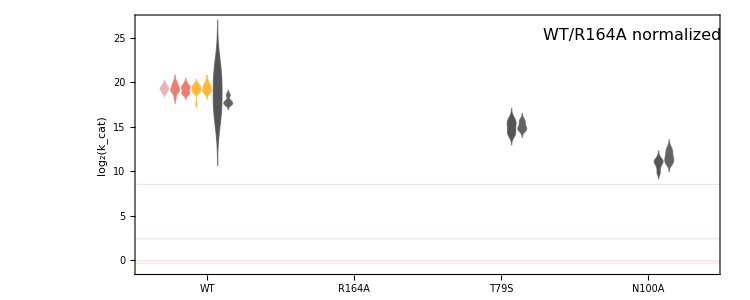

Final normalization factors:

<|190117_S3_d1_MeP_1_GlyScan.csv→0.748386,190123_S3_d1_MeP_1_GlyScan.csv→0.53202,190314_S3_d1_MeP_1_ValScan.csv→2.33315,190318_S3_d1_MeP_1_ValScan.csv→1.19034,190321_S2_d2_MeP_1_ValScan.csv→1.4095,190913_S2_d1_MeP_1_SlowMeP.csv→0.785926,190913_S3_d1_MeP_1_SlowMeP.csv→1.00776,190522_S2_d1_MeP_1_SlowChip.csv→3.34283,190605_S2_d1_MeP_1_SlowChip.csv→1.09634|>

```mathematica
datasetsIn=DeleteDuplicates[Flatten[Values[Normal[groupedbyMutant[All,All,"UniqueExptID"]]]]];

(* separate fast and slow/slowest chips *)
fastChips=Select[datasetsIn,StringContainsQ[#,"Slow"]==False&];
slowChips=Select[datasetsIn,StringContainsQ[#,"Slow"]&];

groupedByExperimentWT=groupedbyMutant["WT"][All,{"UniqueExptID",kcatKmKey}][GroupBy["UniqueExptID"]];
fast=groupedByExperimentWT[fastChips];

groupedByExperimentR164A=groupedbyMutant["T79S"][All,{"UniqueExptID",kcatKmKey}][GroupBy["UniqueExptID"]];
slowNorm=groupedByExperimentR164A[slowChips];

Print["Below is the WT median for the fast chips only:"];
wtMedian=Median[(Join@@Values[Normal[fast[All,All,kcatKmKey]]])]

Print["Below are the per-chip normalization factors based on the WT median:"];
normalizationDataFast=Association[Table[fastChips[[n]]->If[NumberQ[(Median[Normal[fast[fastChips[[n]],All,kcatKmKey]]]/wtMedian)],Median[Normal[fast[fastChips[[n]],All,kcatKmKey]]]/wtMedian,1.0],{n,1,Length[fastChips]}]]

Print["Below is the R164A median for the slow chips only:"];
r164aMedian=Median[(Join@@Values[Normal[slowNorm[All,All,kcatKmKey]]])]

Print["Below are the per-chip normalization factors based on the R164A median:"]
normalizationDataSlow=Association[Table[slowChips[[n]]->If[NumberQ[(Median[Normal[slowNorm[slowChips[[n]],All,kcatKmKey]]]/r164aMedian)],Median[Normal[slowNorm[slowChips[[n]],All,kcatKmKey]]]/r164aMedian,1.0],{n,1,Length[slowChips]}]]

normalizationDataTemp=Join[normalizationDataFast,normalizationDataSlow];

(* apply corrections to both fast and slow datasets *)
normed1=culled[All,Append[#,"kcat/Km_Norm1"->#["kcat/Km"]/normalizationDataTemp[#UniqueExptID]]&];

groupedByExperimentNorm1=normed1[GroupBy["UniqueExptID"]];

tempGroupNorm1=Table[groupedByExperimentNorm1[n][GroupBy["MutantID"]],{n,1,Length[groupedByExperimentNorm1]}];

afterNorm1=DistributionChart[Transpose@Table[{Log[2,Normal[tempGroupNorm1[[n]]["WT"][All,"kcat/Km_Norm1"]]]
,Log[2,Normal[tempGroupNorm1[[n]]["R164A"][All,"kcat/Km_Norm1"]]],Log[2,Normal[tempGroupNorm1[[n]]["T79S"][All,"kcat/Km_Norm1"]]],Log[2,Normal[tempGroupNorm1[[n]]["N100A"][All,"kcat/Km_Norm1"]]]},{n,1,Length[tempGroupNorm1]}],AspectRatio->0.4,ImageSize->750,Frame->True,FrameStyle->Directive[16,Black,FontFamily->"Arial"],BarSpacing->{0.2,5},ChartStyle->Table[If[groupedByExperimentNorm1[n,1,"ChipType"]≠"SlowChip",ColorData[24,n/2],GrayLevel[n/18]],{n,1,Length[groupedByExperimentNorm1]}],ChartLabels->{{"WT","R164A","T79S","N100A"},None},GridLines->{None,Log[2,{373.2,5.3,0.955,0.8125}]},GridLinesStyle->Directive[Darker[Red],Opacity[0.2]]];

(* now normalize fast and slow using R164A (all fast vs. all slow *)
fastMedian=Median[normed1[Select[#ChipType≠"SlowChip"&]][GroupBy["MutantID"]]["T79S"][All,"kcat/Km_Norm1"]]
slowMedian=Median[normed1[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]]["T79S"][All,"kcat/Km_Norm1"]]

secondCorr=<|"SlowChip"->slowMedian/(Mean[{fastMedian,slowMedian}]),"SlowestChip"->slowMedian/(Mean[{fastMedian,slowMedian}]),"ValScan"->fastMedian/(Mean[{fastMedian,slowMedian}]),"GlyScan"->fastMedian/(Mean[{fastMedian,slowMedian}])|>

(* apply second (R164A fast/slow) normalization to both fast and slow datasets *)
normed2=normed1[All,Append[#,"kcat/Km_Norm2"->#["kcat/Km_Norm1"]/secondCorr[#ChipType]]&];

groupedByExperimentNorm2=normed2[GroupBy["UniqueExptID"]];

tempGroupNorm2=Table[groupedByExperimentNorm2[n][GroupBy["MutantID"]],{n,1,Length[groupedByExperimentNorm2]}];

afterNorm2=DistributionChart[Transpose@Table[{Log[2,Normal[tempGroupNorm2[[n]]["WT"][All,"kcat/Km_Norm2"]]]
,Log[2,Normal[tempGroupNorm2[[n]]["R164A"][All,"kcat/Km_Norm2"]]],Log[2,Normal[tempGroupNorm2[[n]]["T79S"][All,"kcat/Km_Norm2"]]],Log[2,Normal[tempGroupNorm2[[n]]["N100A"][All,"kcat/Km_Norm2"]]]},{n,1,Length[tempGroupNorm2]}],AspectRatio->0.4,ImageSize->750,Frame->True,FrameStyle->Directive[16,Black,FontFamily->"Arial"],BarSpacing->{0.2,5},ChartStyle->Table[If[groupedByExperimentNorm2[n,1,"ChipType"]≠"SlowChip",ColorData[24,n/2],GrayLevel[n/18]],{n,1,Length[groupedByExperimentNorm2]}],ChartLabels->{{"WT","R164A","T79S","N100A"},None},GridLines->{None,Log[2,{373.2,5.3,0.955,0.8125}]},GridLinesStyle->Directive[Darker[Red],Opacity[0.2]],FrameLabel->{None,"log_2(k_cat)"},Epilog->Inset[Style["WT/R164A normalized",16],Scaled[{0.85,0.92}]]]

(* multiply first and second normalization factors to get final normalization factors, for analysis below *)
Print[Style["Final normalization factors:",Bold]]
normalizationData=Join[normalizationDataFast*secondCorr["ValScan"],normalizationDataSlow*secondCorr["SlowChip"]]

(* not normalizing *)

(*normalizationData=<|"190407_S3d1PafA_GlyScan_cMUP_190918chipCorrected.csv"->1.0,"181119_S2d2_PafA_GlyScan_cMUP_190918chipCorrected.csv"->1.0,"180614_S3d1_PafA_GlyScan_cMUP_withEconc_190918chipCorrected.csv"->1.0,"180614_S2d1_PafA_GlyScan_cMUP_withEconc_190918chipCorrected.csv"->1.0,"180710_S3d1_PafA_GlyScan_cMUP_081118_chipCorrected_190918chipCorrected.csv"->1.0,"180225_S2d2_PafA_ValScan_cMUP_180924_chipCorrected_190918chipCorrected.csv"->1.0,"180302_S2d3_PafA_ValScan_cMUP_180924_chipCorrected_190918chipCorrected.csv"->1.0,"180402_S4d3_PafA_ValScan_cMUP_180924_chipCorrected_190918chipCorrected.csv"->1.0,"180522_S3d2_PafA_ValScan_cMUP_pH8_180924_chipCorrected_190918chipCorrected.csv"->1.0,"190205_S3d1_PafA_ValScan_cMUP_190918chipCorrected.csv"->1.0,"180528_S3d1_PafA_ValScan_cMUP_190918chipCorrected.csv"->1.0,"180531_S2d1PafA_GlyScan_cMUP_190918chipCorrected.csv"->1.0,"190305_S3d1_PafA_GlyScan_cMUP_190918chipCorrected.csv"->1.0,"190605_S2d1PafA_cMUP_SlowChip_190918chipCorrected.csv"->1.0,"190626_S2d1PafA_cMUP_SlowChip_190918chipCorrected.csv"->1.0,"190630_S2d1PafA_cMUP_SlowChip_190918chipCorrected.csv"->1.0,"190609_S2d1PafA_cMUP_SlowChip_190918chipCorrected.csv"->1.0,"190424_S2d1PafA_cMUP_SlowChip_190918chipCorrected.csv"->1.0|>*)
```

#### Aggregating WT data across experiments, applying normalization factors:

Apply the calculated WT normalization factors to each dataset (on kcat) and plot histograms of the WT kcat values before and after this correction, to assess improvement:

{1.33925×10^6,1.10213×10^6,2.0025×10^6,998408.,1.48192×10^6,1.31692×10^6,1.56015×10^6,1.1174×10^6,1.73766×10^6,1.59478×10^6,2.25633×10^6,1.42389×10^6,1.78639×10^6,1.07451×10^6,1.44904×10^6,655103.,797082.,1.06803×10^6,573370.,847326.,1.08165×10^6,756054.,393691.,635664.,890997.,635160.,603010.,1.22277×10^6,756740.,704518.,559414.,363680.,848326.,942196.,966586.,719377.,1.08967×10^6,615791.,685970.,1.38306×10^6,1.02364×10^6,602677.,776816.,572976.,580623.,1.40726×10^6,1.02874×10^6,1.16647×10^6,592166.,987545.,546360.,574433.,398664.,701578.,511711.,535327.,500828.,667810.,375224.,432275.,345031.,386595.,665507.,449862.,366502.,533826.,351666.,146083.,681675.,277647.,400002.,275276.,593768.,210000.,346742.,337918.,278313.,322301.,409465.,321531.,460314.,248298.,239334.,423633.,466222.,490331.,282123.,408070.,5.84813×10^6,201396.,224594.,266802.,425315.}

603010.

48.8968

95% confidence bounds on fitted WT kcat and KM parameters:

{210000.,2.0025×10^6}

{12.6065,397.966}

Aggregated WT kcat values, before correction:

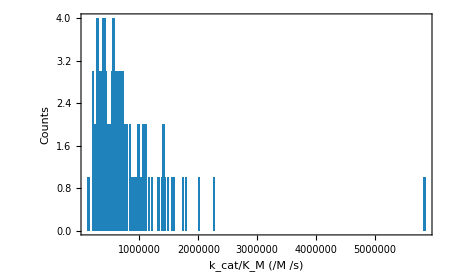

{195198.,1.21734×10^6}

Aggregated kcat values, after correction:

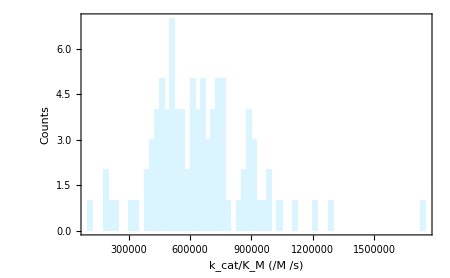

Aggregated kcat values, before and after correction overlaid:

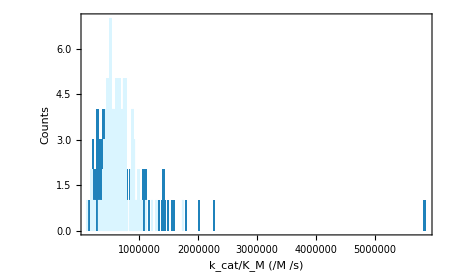

```mathematica
normalizingMutant="WT";

allWTkcatKmValues=Normal[groupedbyMutant[normalizingMutant][All,kcatKmKey]]

allWTkcatValues=Normal[groupedbyMutant[normalizingMutant][All,kcatKey]];

allWTKmValues=Normal[groupedbyMutant[normalizingMutant][All,KmKey]];

wtMedian=Median[allWTkcatKmValues]

KmMedian=Median[allWTKmValues]

(* calculate 95% confidence bounds on both WT parameters *)
Print["95% confidence bounds on fitted WT kcat and KM parameters:"]
wtkcatCIs=Quantile[allWTkcatKmValues,{0.025,0.975}]
wtKmCIs=Quantile[allWTKmValues,{0.025,0.975}]

(* plot distribution of WT Ki values *)
Print["Aggregated WT kcat values, before correction:"]
histPreCorrection=Histogram[allWTkcatKmValues,{25000},PlotRange->All,ChartStyle->ColorData[16,6],Frame->True,Axes->False,FrameStyle->Directive[Black,18],FrameLabel->{"k_cat/K_M (/M /s)","Counts"},ImageSize->450]

normalizedWTkcatKmvalues=Table[Normal[groupedbyMutant[normalizingMutant][n,kcatKmKey]]/normalizationData[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]]],{n,1,Length[allWTkcatValues]}];

normalizedWTkcatvalues=Table[Normal[groupedbyMutant[normalizingMutant][n,kcatKey]]/normalizationData[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]]],{n,1,Length[allWTkcatValues]}];

wtNormalizedkcatCIs=Quantile[normalizedWTkcatKmvalues,{0.025,0.975}]

Print["Aggregated kcat values, after correction:"]
histPostCorrection=Histogram[normalizedWTkcatKmvalues,{25000},PlotRange->All,ChartStyle->ColorData[16,5],Frame->True,Axes->False,FrameStyle->Directive[Black,18],FrameLabel->{"k_cat/K_M (/M /s)","Counts"},ImageSize->450]

Print["Aggregated kcat values, before and after correction overlaid:"]
Show[histPreCorrection,histPostCorrection]

kobsExptIndex=2;

kobsWT=Table[Normal[groupedbyMutant[normalizingMutant][n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationData[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]]]*Normal[groupedbyMutant[normalizingMutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[groupedbyMutant[normalizingMutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]),{n,1,Length[allWTkcatKmValues]}];

wtDataNormAll=Table[{normalizedWTkcatvalues[[n]],allWTKmValues[[n]],normalizedWTkcatKmvalues[[n]],kobsWT[[n]]},{n,1,Length[allWTkcatValues]}];
```

#### Generate an overlaid plot of the wild-type Michaelis-Menten fits for coplotting with mutant Michaelis-Menten fits, to aid interpretation of p-values:

Now want to look at the fitted WT Michaelis-Menten curves overlaid. Plotting all the individual curves in light gray, with the median curve overlaid in dark gray, and curves corresponding to the 99% confidence bounds shown as intermediate gray curves:

```mathematica
(*curves=Table[RandomChoice[normalizedWTkcatvalues]*RandomReal[NormalDistribution[1.0,0.01]]*sub/(RandomChoice[allWTKmValues]*RandomReal[NormalDistribution[1.0,0.01]]+sub),{n,1,200}];*)

curves=Table[normalizedWTkcatvalues[[n]]*sub/(allWTKmValues[[n]]+sub),{n,1,Length[normalizedWTkcatvalues]}];
curvesKm=Table[1.0*sub/(allWTKmValues[[n]]+sub),{n,1,Length[normalizedWTkcatvalues]}];
```

{9.23855,167.596}

{17.4522,269.783}

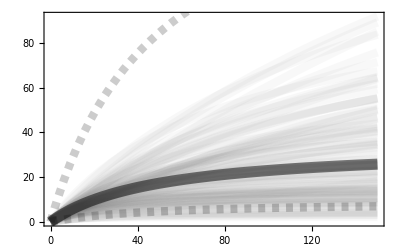

```mathematica
densityFilling1=Plot[curves,{sub,0,150},PlotStyle->Directive[Gray,Thickness[0.015],Opacity[0.05]],PlotPoints->2,Frame->True,Axes->False];

kcatResampled=Quantile[Table[Median[RandomChoice[normalizedWTkcatvalues,5]],{526}],{0.01,0.99}]

KmResampled=Quantile[Table[Median[RandomChoice[allWTKmValues,5]],{526}],{0.01,0.99}]

densityFilling=Show[densityFilling1,Plot[Median[normalizedWTkcatvalues]*sub/(Median[allWTKmValues]+sub),{sub,0,150},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.02],Opacity[0.5]]],Plot[kcatResampled[[1]]*sub/(Median[allWTKmValues]+sub),{sub,0,150},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.015],Dashed,Opacity[0.2]]],Plot[kcatResampled[[2]]*sub/(Median[allWTKmValues]+sub),{sub,0,150},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.015],Dashed,Opacity[0.2]]]]

densityFillingKm=Plot[curvesKm,{sub,0,150},PlotStyle->Directive[Gray,Thickness[0.015],Opacity[0.02]],PlotPoints->2,Frame->True,Axes->False,PlotRange->{0,All}];
```

#### Some code to facilitate automatic plotting and legending (evaluate cell below):

Just lists of colors, plotmarkers, and dashing types, so that each experiment gets its own plot marker, color, and dashing type:

```mathematica
xticks={{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};
xticks2={{{0.01,0},{0.1,0.1},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};

colorMap=Association[Table[datasetsIn[[n]]->ColorData[24,n-1],{n,1,Length[datasetsIn]}]]

plotMarkerList={●,○,◆,◇,■,□,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●};

dashingList={Dashing[None],Dashing[0.05],Dashing[0.015],Dashing[0.03],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};

dashingListLeg={Dashing[None],Dashing[0.05*5],Dashing[0.015*5],Dashing[0.03*5],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};
```

<|190117_S3_d1_MeP_1_GlyScan.csv→RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],190123_S3_d1_MeP_1_GlyScan.csv→RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],190314_S3_d1_MeP_1_ValScan.csv→RGBColor[1., 0.7215686274509804, 0.2196078431372549],190318_S3_d1_MeP_1_ValScan.csv→RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],190321_S2_d2_MeP_1_ValScan.csv→RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],190913_S2_d1_MeP_1_SlowMeP.csv→RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],190913_S3_d1_MeP_1_SlowMeP.csv→RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],190522_S2_d1_MeP_1_SlowChip.csv→RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],190605_S2_d1_MeP_1_SlowChip.csv→RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862]|>

```mathematica
expIndexAssociation=<|"190117_S3_d1_MeP_1_GlyScan.csv"->1,"190123_S3_d1_MeP_1_GlyScan.csv"->2,"190314_S3_d1_MeP_1_ValScan.csv"->3,"190318_S3_d1_MeP_1_ValScan.csv"->4,"190321_S2_d2_MeP_1_ValScan.csv"->5,"190913_S2_d1_MeP_1_SlowMeP.csv"->6,"190913_S3_d1_MeP_1_SlowMeP.csv"->7,"190522_S2_d1_MeP_1_SlowChip.csv"->8,"190605_S2_d1_MeP_1_SlowChip.csv"->9|>
```

<|190117_S3_d1_MeP_1_GlyScan.csv→1,190123_S3_d1_MeP_1_GlyScan.csv→2,190314_S3_d1_MeP_1_ValScan.csv→3,190318_S3_d1_MeP_1_ValScan.csv→4,190321_S2_d2_MeP_1_ValScan.csv→5,190913_S2_d1_MeP_1_SlowMeP.csv→6,190913_S3_d1_MeP_1_SlowMeP.csv→7,190522_S2_d1_MeP_1_SlowChip.csv→8,190605_S2_d1_MeP_1_SlowChip.csv→9|>

#### Bootstrap functions (for p-value calculation and parameter error estimates) (evaluate hidden cell below):

'bsMedian' returns p-values for the following parameters, in the same order: {kcat, KM, kcat/KM}

```mathematica
Needs["HypothesisTesting`"]

bsMedianIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMedian[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=median2[mutantKIswithCIs];

If[Head[weightedMean]==Median,Return[{Indeterminate,Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=median2[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

bsMeanIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMean[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=Mean[mutantKIswithCIs];

weightedWTMean=Mean[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

(* function for bootstrapping residuals - to get parameter estimate errors *)

bsResidual[fitModel_,numBootstraps_]:=Module[{model,data,residuals,bootstraps,concentrations,reshuffled,newData,newFit,newParams},

(* extract input experimental data from FittedModel *)
model=fitModel;
data=model["Data"];

(* extract residuals *)
residuals=model["FitResiduals"];

(* reshuffle residuals and bootstrap (looped) *)
bootstraps=Table[
concentrations=data[[All,1]];

reshuffled=RandomChoice[residuals,Length[residuals]];

newData=Table[{concentrations[[n]],model[concentrations[[n]]]+reshuffled[[n]]},{n,1,Length[concentrations]}];

newFit=NonlinearModelFit[newData,{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate];

newParams=newFit["BestFitParameters"];

{Vmax/.newParams,KM/.newParams},{numBootstraps}]

]

bsStdDevIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsStdDev[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=StandardDeviation[mutantKIswithCIs];

If[Head[weightedMean]==StandardDeviation,Return[{Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=StandardDeviation[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,3}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1,

Return[checkpoint1],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,3}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01,

Return[checkpoint2],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,3}];

Return[checkpoint3]]

];

]

colorPVal[pvalue_,cutoff_]:=If[pvalue≠"N/A",Which[pvalue<cutoff&&pvalue≠0.,Style[ToString[pvalue],Bold,ColorData[20,8]],pvalue==0.,Style["<"<>ToString[1.0/numStatsBootstraps],Bold,ColorData[20,8]],pvalue≥cutoff,ToString[pvalue]],"N/A"]
```

#### Structure mapping function:

```mathematica
pafa=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb",ColorFunction->Function[{x},Directive[GrayLevel[0.8],Opacity[0.7]]]];

seq=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","Sequence"];

seqJoined=Join@@{Table[{n+23,StringTake[seq[[1]],{n}]},{n,1,StringLength[seq[[1]]]}],Table[{n+374,StringTake[seq[[2]],{n}]},{n,1,StringLength[seq[[2]]]}]};

coords=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","ResidueCoordinates"];

pafaAS=Import["/Users/craig/Dropbox/HTMEK_processing/desktop_move_200110/pafa_active_site_wLigands.pdb",ColorFunction->Function[{x},GrayLevel[0.8]]];

joined=Join[coords[[1]],coords[[2]]];

coordsJoined=joined;

cAlphaAssociation=Join[AssociationThread[seqJoined[[All,1]],coordsJoined[[All,2]]],Association[{21->{2535.,-1901.6,5793.},22->{2535.,-1901.6,5793.},23->{2535.,-1901.6,5793.},373->{-1794.2,-2367.6,1819.9},374->{-1553.7,-2917.8999999999996,1116.},546->{568.5,-1399.9,5539.099999999999}}]];

makeStructureNice[res_,mutation_]:=Module[{test2},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

If[mutation≠"WT",Show[pafa,pafaAS,test2,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500],Show[pafa,pafaAS,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]]

makeStructureNiceDM[res1_,res2_,mutation_]:=Module[{test2,test3},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res1]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

test3=ListPointPlot3D[{cAlphaAssociation[res2]},PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

Show[pafa,pafaAS,test2,test3,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]
```

#### Function for statistical analysis, make aggregate plots, and output a dataset with aggregate plots, kinetic parameters, p-values etc. (evaluate hidden cell below):

```mathematica
(* association containing expression numbers, applied to 1000uM [cMUP] only *)
allData=Join@@datasets;
highestSonly=allData[Select[#ExpIndex==1&]];
allGroupedByMutantFast=highestSonly[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlow=highestSonly[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlowest=highestSonly[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

expressionDataFast=Association[Table[allGroupedByMutantFast[mut,1,"MutantID"]->{Length[allGroupedByMutantFast[mut]],Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantFast[mut]]],Normal[allGroupedByMutantFast[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantFast]}]];

expressionDataSlow=Association[Table[allGroupedByMutantSlow[mut,1,"MutantID"]->{Length[allGroupedByMutantSlow[mut]],Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlow[mut]]],Normal[allGroupedByMutantSlow[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlow]}]];

expressionDataSlowest=Association[Table[allGroupedByMutantSlowest[mut,1,"MutantID"]->{Length[allGroupedByMutantSlowest[mut]],Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlowest[mut]]],Normal[allGroupedByMutantSlowest[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlowest]}]];

(* WT fast and slow chip data separated *)

sortedWTbyChipType=groupedbyMutant["WT"][All,{"UniqueExptID","ChipType",kcatKey,KmKey}][GroupBy["ChipType"]];

fastChipDataWT={#[[2]]/normalizationData[#[[1]]],#[[3]],(#[[2]]/normalizationData[#[[1]]])/((#[[3]])*10^-6)}&/@Values[Join[Normal[sortedWTbyChipType["GlyScan",All,{"UniqueExptID",kcatKey,KmKey}]],Normal[sortedWTbyChipType["ValScan",All,{"UniqueExptID",kcatKey,KmKey}]]]];

slowChipDataWT={#[[2]]/normalizationData[#[[1]]],#[[3]],(#[[2]]/normalizationData[#[[1]]])/((#[[3]])*10^-6)}&/@Values[Normal[sortedWTbyChipType["SlowChip",All,{"UniqueExptID",kcatKey,KmKey}]]];

(* no WT on Slowest Chip *)

(* determine the per-chip replacement value for negative kobs (limit) values *)
(* ALSO ADD INDEX of LOWEST [S] EXPT - important for MeP *)
groupedByExptSlowOnly=slow[GroupBy["UniqueExptID"]];

kobsLimitReplacementValues=Association[Table[groupedByExptSlowOnly[expt,1,"UniqueExptID"]->Median[Select[Table[Normal[groupedByExptSlowOnly[expt,n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationData[groupedByExptSlowOnly[expt,1,"UniqueExptID"]]*(Normal[groupedByExptSlowOnly[expt,n,"AllSubstrateConcs"][[kobsExptIndex]]])*Normal[groupedByExptSlowOnly[expt,n,"AllEnzymeConcs"]][[1]]*10^-9),{n,1,Length[groupedByExptSlowOnly[expt]]}],#>0&]],{expt,1,Length[groupedByExptSlowOnly]}]];

makeAggDataset[mutant_]:=Module[{mutantID,enzymeConcs,expts,chipTypes},

mutantID=Normal[groupedbyMutant[mutant,1,"MutantID"]];

expts=Table[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant[mutant]]}];

exptsTrimmedNames=Table[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant[mutant]]}];

chipTypes=Table[Normal[groupedbyMutant[mutant,n,"ChipType"]],{n,1,Length[groupedbyMutant[mutant]]}];

lbrs=Table[Normal[groupedbyMutant[mutant,n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutant[mutant]]}];

r2s=Table[Normal[groupedbyMutant[mutant,n,"FitR2"]],{n,1,Length[groupedbyMutant[mutant]]}];

(* normalization of fitted kcats (lagoon and chip corrected) to internal WT kcat standard *)
normalizationFactors=normalizationData[#]&/@expts;

chambers=Table[ToExpression[Normal[groupedbyMutant[mutant,n,"Indices"]]],{n,1,Length[groupedbyMutant[mutant]]}];

enzymeConcs=Table[Normal[groupedbyMutant[mutant,n,"AllEnzymeConcs"]][[1]],{n,1,Length[groupedbyMutant[mutant]]}];

(* kobs fits obtained by scaling exponential fit k by normalizationFactor and [E] *)
(*kobs=Table[ToExpression[Normal[groupedbyMutant[mutant,n,"ExponentialFit"]]][[1]]/(normalizationFactors[[n]]*enzymeConcs[[n]]*10^-9),{n,1,Length[groupedbyMutant[mutant]]}];*)

(* kobs determined by scaling linear fit at lowest [S] by [S] and [E] *)
kobsRaw=Table[Normal[groupedbyMutant[mutant,n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationFactors[[n]]*(Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]])*enzymeConcs[[n]]*10^-9),{n,1,Length[groupedbyMutant[mutant]]}];

(* correct negative kobs *)
kobs=Table[If[kobsRaw[[n]]<0,kobsLimitReplacementValues[expts[[n]]],kobsRaw[[n]]],{n,1,Length[groupedbyMutant[mutant]]}];

(* get min and max [S] to plot as gridlines on Km plot *)
highLowSlimits={Min[Select[#[[All,1]],#≠0&]],Max[#[[All,1]]]}&/@ToExpression[Normal[groupedbyMutant[mutant,All,"DataPoints"]]];

(* apply normalization factors directly to kcats, to simplify downstream calculations *)
mutantkcatsRaw=Table[Normal[groupedbyMutant[mutant,n,kcatKey]],{n,1,Length[groupedbyMutant[mutant]]}];
mutantkcatsIn=Table[Normal[groupedbyMutant[mutant,n,kcatKey]]/normalizationFactors[[n]],{n,1,Length[groupedbyMutant[mutant]]}];
mutantkcats=Fold[Replace[#1,#2,Infinity]&,mutantkcatsIn,{_Times->Indeterminate}];

mutantKmsRaw=Normal[groupedbyMutant[mutant,All,KmKey]];

(* check mutant Km data for tight and weak Km limits (Km<KmFlag), and if so, replace with Km=lowest [S]/2 and a limit flag *)
(* modified 20/02/25 *)
mutantKmDataIn=Which[#<(highLowSlimits[[1,1]]/2),{highLowSlimits[[1,1]]/2,-1},#>highLowSlimits[[1,2]]*2,{#,1},(highLowSlimits[[1,1]]/2)≤#≤ highLowSlimits[[1,2]]*2,{#,0}]&/@Normal[groupedbyMutant[mutant,All,KmKey]];

mutantKmData=mutantKmDataIn[[All,1]];

mutantKmLimitTable=mutantKmDataIn[[All,2]];

kcatOverKmRaw=mutantkcatsRaw/(mutantKmData*10^-6);

kcatOverKmData=mutantkcats/(mutantKmData*10^-6);

(* determine if enough Kms are limits to define the aggregate estimate as a limit *)
aggKmLimit=If[Length[Select[mutantKmLimitTable,#==0&]]/Length[mutantKmLimitTable]>0.5,0,Select[mutantKmLimitTable,#≠0&][[1]]];

(* kcat/Km limits *)
kcatKmLimitTable=-Replace[mutantKmLimitTable,1->0,1];

aggkcatKmLimit=If[aggKmLimit≠0&&aggKmLimit≠1,-aggKmLimit,0];

data=ToExpression[Normal[groupedbyMutant[mutant,All,"DataPoints"]]];

dataScaled=Table[Table[{Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"][[i]]],Normal[groupedbyMutant[mutant,n,"AllInitialRates"][[i]]]/(enzymeConcs[[n]]*10^-3)/normalizationFactors[[n]]},{i,1,Length[groupedbyMutant[mutant,n,"AllSubstrateConcs"]]}],{n,1,Length[groupedbyMutant[mutant]]}];

(* generate Michaelis-Menten plots, normalized *)
exptsPlottedXNorm={};
fitPlotNorm=Show[Table[

AppendTo[exptsPlottedXNorm,expts[[n]]];exptCount=Count[exptsPlottedXNorm,expts[[n]]];

Show[ListPlot[dataScaled[[n]],PlotStyle->Directive[colorMap[expts[[n]]]],Frame->True,Axes->False,GridLines->{highLowSlimits[[n]],None},ImageSize->450,PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,Max[DeleteCases[dataScaled[[All,All,2]],Indeterminate,Infinity]]*1.15}},GridLinesStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Rate/[E] (/s)"},PlotMarkers->{plotMarkerList[[exptCount]],Medium}],

Plot[mutantkcats[[n]]*sconc/(mutantKmsRaw[[n]]+sconc),{sconc,0.01,10000},PlotStyle->Directive[colorMap[expts[[n]]],dashingList[[exptCount]]],PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,Max[DeleteCases[dataScaled[[All,All,2]],Indeterminate,Infinity]]*1.15}},Frame->True,Axes->False,GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Rate/[E] (/s)"}]

],{n,1,Length[data]}],

densityFilling,Epilog->{Inset[Style[Normal[groupedbyMutant[mutant,1,"MutantID"]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.87}]],Inset[Style["n="<>ToString[Length[mutantkcats]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.8}]]}];

(* kcat normalized plot, to show spread in KM *)
exptsPlottedXNorm2={};
KmNormPlot=Show[Table[

AppendTo[exptsPlottedXNorm2,expts[[n]]];exptCount=Count[exptsPlottedXNorm2,expts[[n]]];

Show[

Plot[(mutantkcats[[n]]*sconc/(mutantKmsRaw[[n]]+sconc))/mutantkcats[[n]],{sconc,0.0,10000},PlotStyle->Directive[colorMap[expts[[n]]],dashingList[[exptCount]]],PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,1.15}},Frame->True,Axes->False,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Normalized to fitted k_cat"}]

],{n,1,Length[data]}],

densityFillingKm,Epilog->{Inset[Style[Normal[groupedbyMutant[mutant,1,"MutantID"]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.87}]],Inset[Style["n="<>ToString[Length[mutantkcats]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.8}]]}];

merged=Table[{chipTypes[[n]],mutantkcats[[n]],mutantKmData[[n]],kcatOverKmData[[n]]},{n,1,Length[chipTypes]}];

(* modified for KnownMutants *)
fastChipData=Select[merged,#[[1]]=="ValScan"||#[[1]]=="GlyScan"&];
slowChipData=Select[merged,#[[1]]=="SlowChip"&];

slowestChipData=Select[merged,#[[1]]=="SlowestChip"&];

(* bootstrap hypothesis testing - median *)
(* adding 4th element to bootstrap input list to test kobs *)
mutantNormDataAll=Table[{mutantkcats[[n]],mutantKmData[[n]],kcatOverKmData[[n]],kobs[[n]]},{n,1,Length[groupedbyMutant[mutant]]}];
pvaluesMedian=bsMedian[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

(* bootstrap hypothesis testing - mean *)
pvaluesMean=bsMean[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

kcatHistNorm=Histogram[Log[2,{fastChipDataWT[[All,1]],fastChipData[[All,2]],slowChipData[[All,2]],slowestChipData[[All,2]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)) (/s)","Counts"},Epilog->{Inset[Style["k_cat",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[1]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.2,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

KmHist=Histogram[Log[2,{fastChipDataWT[[All,2]],fastChipData[[All,3]],slowChipData[[All,3]],slowestChipData[[All,3]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(K_M) (μM)","Counts"},Epilog->{Inset[Style["K_M",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[2]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.2,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

kcatKmHist=Histogram[Log[2,{fastChipDataWT[[All,3]],fastChipData[[All,4]],slowChipData[[All,4]],slowestChipData[[All,4]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)/K_M) (/M /s)","Counts"},Epilog->{Inset[Style["k_cat/K_M",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[3]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.25,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&][[All,1]];
lbrsSlow=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowChip"&][[All,1]];
lbrsSlowest=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowestChip"&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast])/(Length[lbrsFast]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow])/(Length[lbrsSlow]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest])/(Length[lbrsSlowest]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},FrameLabel->{"Local Limit of Quantification","Counts"},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];

(* kcat vs. Km plot *)
kcatvsKmPlot=ListPlot[Table[Style[Log[2,{mutantkcats[[n]],mutantKmData[[n]]}],colorMap[expts[[n]]]],{n,1,Length[mutantkcats]}],PlotStyle->PointSize[0.03],Frame->True,ImageSize->440*0.8,Axes->False,PlotRange->{{-1,10},{-1,10}},AspectRatio->1,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)) (/s)","log_2(K_M) (μM)"}];

(* replicate plot as a function of experiment - kcat *)
getExptMeanIn=Gather[Table[{expts[[expt]],kcatOverKmData[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
getExptMeanInUnnormed=Gather[Table[{expts[[expt]],kcatOverKmRaw[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
(* calculate per-experiment mean *)
getExptMean={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanIn;
getExptMeanUnnormed={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanInUnnormed;

forRepPlotNorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanIn[[mut,n,1]]],getExptMeanIn[[mut,n,2]]},Darker[colorMap[getExptMeanIn[[mut,n,1]]]]],getExptMeanIn[[mut,n,2]],getExptMeanIn[[mut,n,3]],Darker[colorMap[getExptMeanIn[[mut,n,1]]]],getExptMeanIn[[mut,n,1]]},{n,1,Length[getExptMeanIn[[mut]]]}],{mut,1,Length[getExptMeanIn]}],1];

forRepPlotNormMean=Table[{Style[Callout[{expIndexAssociation[getExptMean[[expt,1]]],getExptMean[[expt,2]]},getExptMean[[expt,3]]],colorMap[getExptMean[[expt,1]]]],getExptMean[[expt,2]],getExptMean[[expt,3]],colorMap[getExptMean[[expt,1]]],getExptMean[[expt,1]]},{expt,1,Length[getExptMean]}];

forRepPlotUnnorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanInUnnormed[[mut,n,1]]],getExptMeanInUnnormed[[mut,n,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanInUnnormed[[mut,n,2]],getExptMeanInUnnormed[[mut,n,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanInUnnormed[[mut,n,1]]},{n,1,Length[getExptMeanInUnnormed[[mut]]]}],{mut,1,Length[getExptMeanInUnnormed]}],1];

forRepPlotUnnormMean=Table[{Style[{expIndexAssociation[getExptMeanUnnormed[[expt,1]]],getExptMeanUnnormed[[expt,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanUnnormed[[expt,2]],getExptMeanUnnormed[[expt,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanUnnormed[[expt,1]]},{expt,1,Length[getExptMeanUnnormed]}];

replicatesVexpt=Show[ListLogPlot[forRepPlotUnnormMean[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.025]],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment",Style["Normalized k_cat/K_M (M^-1 s^-1)",SingleLetterItalics->False]},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,9.5},{100.0,1 10^7}},ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{7.5,-1 10^4},{9.5,1*^4}]},Epilog->Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.2]]},{Style["Unnorm.",16]}],Scaled[{0.8,0.85}]]],ListLogPlot[forRepPlotUnnorm[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.01]],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"],ListLogPlot[forRepPlotNormMean[[All,1]],PlotStyle->PointSize[0.025],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","Normalized k_cat (/s)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,19},{0.01,2000.0}},ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{12,-1 10^4},{16,1*^4}]}],ListLogPlot[forRepPlotNorm[[All,1]],PlotStyle->PointSize[0.01],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"]];

(* replicate plot as a function of experiment - Km *)
getExptMeanInKm=Gather[Table[{expts[[expt]],mutantKmData[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
(* calculate per-experiment mean *)
getExptMeanKm={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanInKm;

forRepPlotNormKm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanInKm[[mut,n,1]]],getExptMeanInKm[[mut,n,2]]},Darker[colorMap[getExptMeanInKm[[mut,n,1]]]]],getExptMeanInKm[[mut,n,2]],getExptMeanInKm[[mut,n,3]],Darker[colorMap[getExptMeanInKm[[mut,n,1]]]],getExptMeanInKm[[mut,n,1]]},{n,1,Length[getExptMeanInKm[[mut]]]}],{mut,1,Length[getExptMeanInKm]}],1];

forRepPlotNormMeanKm=Table[{Style[Callout[{expIndexAssociation[getExptMeanKm[[expt,1]]],getExptMeanKm[[expt,2]]},getExptMeanKm[[expt,3]]],colorMap[getExptMeanKm[[expt,1]]]],getExptMeanKm[[expt,2]],getExptMeanKm[[expt,3]],colorMap[getExptMeanKm[[expt,1]]],getExptMeanKm[[expt,1]]},{expt,1,Length[getExptMeanKm]}];

replicatesVexptKm=Show[ListLogPlot[forRepPlotNormMeanKm[[All,1]],PlotStyle->PointSize[0.025],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","Normalized K_M (μM)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,16},{0.01,2000.0}},PlotRangePadding->None,ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{12,-1 10^4},{16,1*^4}]}],ListLogPlot[forRepPlotNormKm[[All,1]],PlotStyle->PointSize[0.01],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"]];

exptsPlottedLegend={};

repData=Replace[Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["[E] (nM)",Bold],Style["k_(cat,Norm.) (/s)",Bold],Style["K_M (μM)",Bold],Style["K_M Limit",Bold],Style["k_cat/K_(M,Norm.)",Bold],Style["k_obs",Bold],Style["p-value",Bold],Style["R^2",Bold],Style["LBR",Bold]}},

Table[

AppendTo[exptsPlottedLegend,expts[[n]]];exptCountLeg=Count[exptsPlottedLegend,expts[[n]]];

{exptsTrimmedNames[[n]],chipTypes[[n]],Row[{Style[plotMarkerList[[exptCountLeg]],colorMap[expts[[n]]]]," ",Graphics[{dashingListLeg[[exptCountLeg]],colorMap[expts[[n]]],Line[{{0,0},{0.2,0}}]},AspectRatio->0.3,ImageSize->50]}],chambers[[n,1]],chambers[[n,2]],Round[enzymeConcs[[n]],0.01],Round[mutantkcats[[n]],0.1],Round[mutantKmData[[n]],0.1],mutantKmLimitTable[[n]],Round[kcatOverKmData[[n]],1000.],Round[kobs[[n]],1000.],"",Round[r2s[[n]],0.01],Round[lbrs[[n]],0.1]},{n,1,Length[groupedbyMutant[mutant]]}],

Table[Style[#,Pink]&/@{StringTake[tooSlow[mutant,n,"UniqueExptID"],11],tooSlow[mutant,n,"ChipType"],"",ToExpression[tooSlow[mutant,n,"Indices"]][[1]],ToExpression[tooSlow[mutant,n,"Indices"]][[2]],Round[Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],0.01],"","","","",If[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]])<0,kobsLimitReplacementValues[tooSlow[mutant,n,"UniqueExptID"]],Round[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),100]],"",Round[tooSlow[mutant,n,"FitR2"],0.01],Round[tooSlow[mutant,n,"LocalBackgroundRatio"],0.1]},{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}],

{{Style["Median k_cat",Bold],"","","","","",If[pvaluesMedian[[1]]<0.01,Style[Round[Median[Replace[mutantkcats,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[mutantkcats,Indeterminate->Nothing,1]],0.1]],"","","","",colorPVal[pvaluesMedian[[1]],0.01],""},{Style["Median K_M",Bold],"","","","","","",If[pvaluesMedian[[2]]<0.01,Style[Round[Median[Replace[mutantKmData,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[mutantKmData,Indeterminate->Nothing,1]],0.1]],"","","",colorPVal[pvaluesMedian[[2]],0.01],""},{Style["Median k_cat/K_M",Bold],"","","","","","","","",If[pvaluesMedian[[3]]<0.01,Style[Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000],ColorData[20,8]],Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000]],Round[Median[Replace[kobs,Indeterminate->Nothing,1]],1000],colorPVal[pvaluesMedian[[3]],0.01],""}},

{{"","","","","","","","","","","","","",""}},

{{Style["Median WT k_cat",Bold],"","","","","",Round[Median[Replace[wtDataNormAll[[All,1]],Indeterminate->Nothing,1]],0.1],"","","","","","",""},{Style["Median WT K_M",Bold],"","","","","","",Round[Median[Replace[wtDataNormAll[[All,2]],Indeterminate->Nothing,1]],0.1],aggKmLimit,"","","","",""},{Style["Median WT k_cat/K_M",Bold],"","","","","","","","",Round[Median[Replace[wtDataNormAll[[All,3]],Indeterminate->Nothing,1]],1000],Round[Median[Replace[wtDataNormAll[[All,4]],Indeterminate->Nothing,1]],1000],"","",""}}

],_If->Indeterminate,Infinity];

paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["k_cat (s^-1)",Bold],If[pvaluesMedian[[1]]<0.01,Style[Round[Median[Replace[mutantkcats,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[mutantkcats,Indeterminate->Nothing,1]],0.1]],Round[StandardDeviation[Replace[mutantkcats,Indeterminate->Nothing,1]],0.1],colorPVal[pvaluesMedian[[1]],0.01],Length[Replace[mutantkcats,Indeterminate->Nothing,1]]},{Style["K_M (μM)",Bold],If[pvaluesMedian[[2]]<0.01,Style[Round[Median[Replace[mutantKmData,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[mutantKmData,Indeterminate->Nothing,1]],0.1]],Round[StandardDeviation[Replace[mutantKmData,Indeterminate->Nothing,1]],0.1],colorPVal[pvaluesMedian[[2]],0.01],Length[Replace[mutantKmData,Indeterminate->Nothing,1]]},{Style["k_cat/K_M (M^-1 s^-1)",Bold],If[pvaluesMedian[[3]]<0.01,Style[Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000],ColorData[20,8]],Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000]],Round[StandardDeviation[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000],colorPVal[pvaluesMedian[[3]],0.01],Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",expressionDataFast[mutant][[1]]},{Style["Expressed (>0.3nM)"],"","","",expressionDataFast[mutant][[2]]},{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast]+Length[lbrsFastlowR2])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow]+Length[lbrsSlowlowR2])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])]}

},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=If[mutant≠"N100A/R164A",makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant],makeStructureNiceDM[100,164,"N100A/R164A"]];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

forCSV=Join[Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutantID,"Experiment"->expts[[n]],"ChipType"->chipTypes[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"EnzymeConc"->enzymeConcs[[n]],"AllSubstrateConcs"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllInitialRates"]]],"kcat"->mutantkcatsRaw[[n]],"kcatNormalized"->mutantkcats[[n]],"kcatLimit"->0,"KMFit"->mutantKmsRaw[[n]],"KMLimitValue"->mutantKmData[[n]],"KMLimit"->mutantKmLimitTable[[n]],"FitRSquared"->groupedbyMutant[mutant,n,"FitR2"],"kcatFitError"->groupedbyMutant[mutant,n,"fit_mm_kcat_param_error"],"KMFitError"->groupedbyMutant[mutant,n,"fit_mm_KM_param_error"],"kcatoverKMFitError"->(Around[mutantKmData[[n]],groupedbyMutant[mutant,n,"fit_mm_kcat_param_error"]]/(Around[mutantKmData[[n]],groupedbyMutant[mutant,n,"fit_mm_KM_param_error"]]*10^-6))["Uncertainty"],

"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],"KMMean"->Mean[mutantKmData],"KMMedian"->median2[mutantKmData],

"kcat/KMNorm"->kcatOverKmData[[n]],"kobs"->kobsRaw[[n]],"kobsNegCorrected"->kobs[[n]],"kcat/KMNormMean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMedian"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KMBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/KMBootstrapHypothesisTestMedian"->pvaluesMedian[[3]],"kobsBootstrapHypothesisTestMedian"->pvaluesMedian[[4]],

"Log2StdDevkcat"->If[Length[Replace[mutantkcats,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[mutantkcats,Indeterminate->Nothing,1]]],""],"Log2StdDevKM"->If[Length[Replace[mutantKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[mutantKmData,Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KM"->If[Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[kcatOverKmData,Indeterminate->Nothing,1]]],""],

"Log2StdDevkcat/KMLimit"->If[Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[kcatOverKmData,Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KMBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/KMBootstrapHypothesisTestMean"->pvaluesMean[[3]],"kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->Length[mutantkcatsIn],"LBR"->lbrs[[n]],"FractionCulled"->fractionCulled,"StdDevkcat"->If[Length[Replace[mutantkcats,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[mutantkcats,Indeterminate->Nothing,1]],""],"StdDevKM"->If[Length[Replace[mutantKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[mutantKmData,Indeterminate->Nothing,1]],""],"StdDevkcat/KM"->If[Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[kcatOverKmData,Indeterminate->Nothing,1]],""],"kcat/KMLimit"->kcatKmLimitTable[[n]],"kcatAggLimit"->0,"KMAggLimit"->aggKmLimit,"kcat/KMAggLimit"->aggkcatKmLimit,"KMMedianLimit"->median2[mutantKmData],"KMMeanLimit"->Mean[mutantKmData],"kcat/KMNormMedianLimit"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMeanLimit"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]]

}],{n,1,Length[groupedbyMutant[mutant]]}],

Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutantID,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],"AllSubstrateConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"kcat"->"","kcatNormalized"->"","kcatLimit"->"","KMFit"->"","KMLimitValue"->"","KMLimit"->"","FitRSquared"->"","kcatFitError"->"","KMFitError"->"","kcatoverKMFitError"->"",

"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],"KMMean"->Mean[mutantKmData],"KMMedian"->median2[mutantKmData],

"kcat/KMNorm"->"","kobsRaw"->((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),"kobsNegCorrected"->If[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]])<0,kobsLimitReplacementValues[tooSlow[mutant,n,"UniqueExptID"]],((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]])],"kcat/KMNormMean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMedian"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KMBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/KMBootstrapHypothesisTestMedian"->pvaluesMedian[[3]],"kobsBootstrapHypothesisTestMedian"->pvaluesMedian[[4]],

"Log2StdDevkcat"->If[Length[Replace[mutantkcats,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[mutantkcats,Indeterminate->Nothing,1]]],""],"Log2StdDevKM"->If[Length[Replace[mutantKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[mutantKmData,Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KM"->If[Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[kcatOverKmData,Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KMLimit"->If[Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[kcatOverKmData,Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KMBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/KMBootstrapHypothesisTestMean"->pvaluesMean[[3]],"kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->Length[mutantkcatsIn],"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"FractionCulled"->fractionCulled,"StdDevkcat"->If[Length[Replace[mutantkcats,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[mutantkcats,Indeterminate->Nothing,1]],""],"StdDevKM"->If[Length[Replace[mutantKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[mutantKmData,Indeterminate->Nothing,1]],""],"StdDevkcat/KM"->If[Length[Replace[mutantKmData,Indeterminate->Nothing,1]]>1,StandardDeviation[Replace[kcatOverKmData,Indeterminate->Nothing,1]],""],"kcat/KMLimit"->-1,"kcatAggLimit"->0,"KMAggLimit"->aggKmLimit,"kcat/KMAggLimit"->aggkcatKmLimit,"KMMedianLimit"->median2[mutantKmData],"KMMeanLimit"->Mean[mutantKmData],"kcat/KMNormMedianLimit"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMeanLimit"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]]

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}]

];

forPDF=Table[Association[{"MutantID"->mutantID,"Experiment"->expts[[n]],"Indices"->chambers[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"Data"->dataScaled[[n]],"EnzymeConc"->enzymeConcs[[n]],"kcat"->mutantkcats[[n]],"kcatNormalized"->mutantkcats[[n]],"FitRSquared"->r2s[[n]],"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],

"Km"->mutantKmData[[n]],"KmLimit"->mutantKmLimitTable[[n]],"KmMean"->Mean[mutantKmData],"KmMedian"->median2[mutantKmData],

"kcat/Km_Norm"->kcatOverKmData[[n]],"kobs"->kobs[[n]],"kcat/Km_Norm_Mean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/Km_Norm_Median"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"FitPlotNorm"->fitPlotNorm,"kcatNormHistogram"->kcatHistNorm,"KmNormPlot"->KmNormPlot,"KmHistogram"->KmHist,"kcat/Km_Histogram"->kcatKmHist,"FractionCulledHist"->lbrHist,"ExpressionHist"->expressionHist,"kcatvsKmPlot"->kcatvsKmPlot,"ReplicatePlot"->replicatesVexpt,"ReplicatePlotKm"->replicatesVexptKm,

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KmBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/Km_BootstrapHypothesisTestMedian"->pvaluesMedian[[3]],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KmBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/Km_BootstrapHypothesisTestMean"->pvaluesMean[[3]],

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]

makeAggDatasetSlow[mutant_]:=Module[{fractionculled},

fractionCulled=1.0;

tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlow=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowest=Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowestChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]];

lbrsFastlowR2=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowlowR2=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowestlowR2=Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowestChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast]+Length[lbrsFastlowR2])/(Length[lbrsFast]+Length[lbrsFastlowR2]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow]+Length[lbrsSlowlowR2])/(Length[lbrsSlow]+Length[lbrsSlowlowR2]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])/(Length[lbrsSlowest]+Length[lbrsSlowestlowR2]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Detection","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Detection","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];

kobsRaw=Table[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),{n,1,Length[tooSlow[mutant]]}];

(* correct negative kobs *)
kobs=Table[If[kobsRaw[[n]]<0,kobsLimitReplacementValues[Normal[tooSlow[mutant,n,"UniqueExptID"]]],kobsRaw[[n]]],{n,1,Length[tooSlow[mutant]]}];

(* bootstrap hypothesis testing - median *)
(* adding 4th element to bootstrap input list to test kobs - adding 1s because function expects a list of length=4, but only kobs can be measured for undetectably slow mutants *)
mutantNormDataAll=Table[{1.0,1.0,1.0,kobs[[n]]},{n,1,Length[tooSlow[mutant]]}];
pvaluesMedian=bsMedian[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

(* bootstrap hypothesis testing - mean *)
pvaluesMean=bsMean[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

repData=Replace[Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["[E] (nM)",Bold],Style["k_(cat,Norm.) (/s)",Bold],Style["K_M (μM)",Bold],Style["K_M Limit",Bold],Style["k_cat/K_(M,Norm.)",Bold],Style["k_obs",Bold],Style["p-value",Bold],Style["R^2",Bold],Style["LBR",Bold]}},

Table[Style[#,Pink]&/@{StringTake[tooSlow[mutant,n,"UniqueExptID"],11],tooSlow[mutant,n,"ChipType"],"",ToExpression[tooSlow[mutant,n,"Indices"]][[1]],ToExpression[tooSlow[mutant,n,"Indices"]][[2]],Round[Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],0.01],"","","","",Round[kobs[[n]],1],"",Round[tooSlow[mutant,n,"FitR2"],0.01],Round[tooSlow[mutant,n,"LocalBackgroundRatio"],0.1]},{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}],

{{Style["Median k_cat",Bold],"","","","","","","","","","","","",""},{Style["Median K_M",Bold],"","","","","","","","","","","","",""},{Style["Median k_cat/K_M",Bold],"","","","","","","",Round[median2[Replace[kobs,Indeterminate->Nothing,1]],1],"","",colorPVal[pvaluesMedian[[4]],0.01]}},

{{"","","","","","","","","","","","","",""}},

{{Style["Median WT k_cat",Bold],"","","","","",Round[median2[Replace[wtDataNormAll[[All,1]],Indeterminate->Nothing,1]],0.1],"","","","","",""},{Style["Median WT K_M",Bold],"","","","","","",Round[median2[Replace[wtDataNormAll[[All,2]],Indeterminate->Nothing,1]],0.1],"","","","",""},{Style["Median WT k_cat/K_M",Bold],"","","","","","","","",Round[median2[Replace[wtDataNormAll[[All,3]],Indeterminate->Nothing,1]],1000],Round[median2[Replace[wtDataNormAll[[All,4]],Indeterminate->Nothing,1]],1],"",""}}

],_If->Indeterminate,Infinity];



paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["k_cat (s^-1)",Bold],"N/A","N/A","N/A",0},{Style["K_M (μM)",Bold],"N/A","N/A","N/A",0},{Style["k_cat/K_M (M^-1 s^-1)",Bold],"N/A","N/A","N/A",0},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",expressionDataFast[mutant][[1]]},{Style["Expressed (>0.3nM)"],"","","",expressionDataFast[mutant][[2]]},{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast]+Length[lbrsFastlowR2])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow]+Length[lbrsSlowlowR2])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])]}},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=If[mutant≠"N100A/R164A",makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant],makeStructureNiceDM[100,164,"N100A/R164A"]];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

forCSV=Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutant,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],"AllSubstrateConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"kcat"->"","kcatNormalized"->"","kcatLimit"->"","KMFit"->"","KMLimitValue"->"","KMLimit"->"","FitRSquared"->Round[tooSlow[mutant,n,"FitR2"],0.01],"kcatFitError"->"","KMFitError"->"","kcatoverKMFitError"->"",

"kcatNormMean"->"","kcatNormMedian"->"","KMMean"->"","KMMedian"->"",

"kcat/KMNorm"->"","kobsRaw"->kobsRaw[[n]],"kobsNegCorrected"->kobs[[n]],"kcat/KMNormMean"->"","kcat/KMNormMedian"->"",

"kcatNormBootstrapHypothesisTestMedian"->"","KMBootstrapHypothesisTestMedian"->"","kcat/KMBootstrapHypothesisTestMedian"->"","kobsBootstrapHypothesisTestMedian"->pvaluesMedian[[4]],

"Log2StdDevkcat"->"","Log2StdDevKM"->"","Log2StdDevkcat/KM"->"","Log2StdDevkcat/KMLimit"->If[Length[Replace[kobs,Indeterminate->Nothing,1]]>1,StandardDeviation[Log[2,Replace[kobs,Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->"","KMBootstrapHypothesisTestMean"->"","kcat/KMBootstrapHypothesisTestMean"->"","kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->0,"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"FractionCulled"->fractionCulled,

"StdDevkcat"->"","StdDevKM"->"","StdDevkcat/KM"->"","kcatLimit"->"","kcat/KMLimit"->-1,"kcatAggLimit"->0,"KMAggLimit"->"","kcat/KMAggLimit"->-1,"KMMedianLimit"->"","KMMeanLimit"->"","kcat/KMNormMedianLimit"->median2[kobs],"kcat/KMNormMeanLimit"->Mean[kobs]

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}];

forPDF=Table[Association[{"MutantID"->mutant,

"FitPlotNorm"->"","kcatNormHistogram"->"","KmNormPlot"->"","KmHistogram"->"","kcat/Km_Histogram"->"","kcatvsKmPlot"->"","ExpressionHist"->expressionHist,"ReplicatePlot"->"","ReplicatePlotKm"->"","FractionCulledHist"->lbrHist,

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]
```

```mathematica
SeedRandom[2020]

Dynamic[mutantIterator]

culledLength=Length[mutantsWithData];
dropLength=Length[unmeasured];

(*culledLength=5;
dropLength=1;*)

start1=AbsoluteTime[];

total=Table[makeAggDataset[mutantsWithData[[mutantIterator]]],{mutantIterator,1,culledLength}];
totalSlow=Table[makeAggDatasetSlow[unmeasured[[mutantIterator]]],{mutantIterator,1,dropLength}];

outForCSV=Join[Table[Values[total[[mutantIterator,1]]],{mutantIterator,1,culledLength}],Table[Values[totalSlow[[mutantIterator,1]]],{mutantIterator,1,dropLength}]];

outForPDF=Join[Flatten[Table[total[[mutantIterator,2]],{mutantIterator,1,culledLength}],1],Flatten[Table[totalSlow[[mutantIterator,2]],{mutantIterator,1,dropLength}],1]];

AbsoluteTime[]-start1
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

StandardDeviation::shlen: The argument {0.117647} should have at least two elements.

StandardDeviation::shlen: The argument {8.49192} should have at least two elements.

StandardDeviation::shlen: The argument {13854.} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

ListPointPlot3D::ldata: Callout[{Missing[KeyAbsent,Null]},WT,{1895.1,-25.,3038.1}] is not a valid dataset or list of datasets.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

1971.04204

Number of mutants with aggregate measurement:

950

{Version,RunDate,MutantID,Experiment,ChipType,Column,Row,EnzymeConc,AllSubstrateConcs,AllInitialRates,kcat,kcatNormalized,kcatLimit,KMFit,KMLimitValue,KMLimit,FitRSquared,kcatFitError,KMFitError,kcatoverKMFitError,kcatNormMean,kcatNormMedian,KMMean,KMMedian,kcat/KMNorm,kobsRaw,kobsNegCorrected,kcat/KMNormMean,kcat/KMNormMedian,kcatNormBootstrapHypothesisTestMedian,KMBootstrapHypothesisTestMedian,kcat/KMBootstrapHypothesisTestMedian,kobsBootstrapHypothesisTestMedian,Log2StdDevkcat,Log2StdDevKM,Log2StdDevkcat/KM,Log2StdDevkcat/KMLimit,kcatNormBootstrapHypothesisTestMean,KMBootstrapHypothesisTestMean,kcat/KMBootstrapHypothesisTestMean,kobsBootstrapHypothesisTestMean,NumCulledReps,LBR,FractionCulled,StdDevkcat,StdDevKM,StdDevkcat/KM,kcat/KMLimit,kcatAggLimit,KMAggLimit,kcat/KMAggLimit,KMMedianLimit,KMMeanLimit,kcat/KMNormMedianLimit,kcat/KMNormMeanLimit}

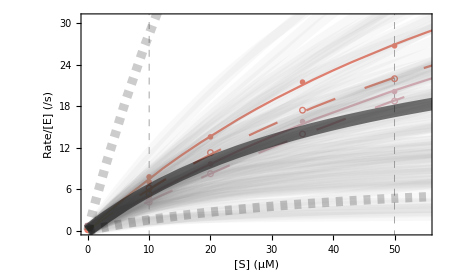
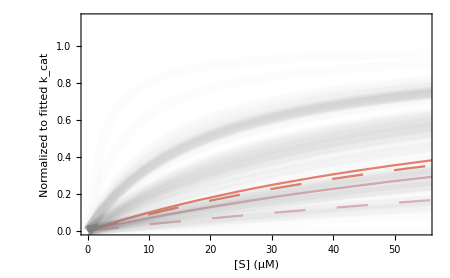
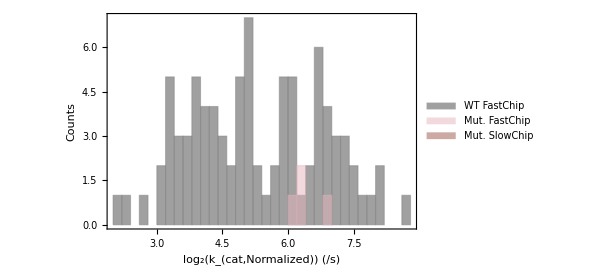
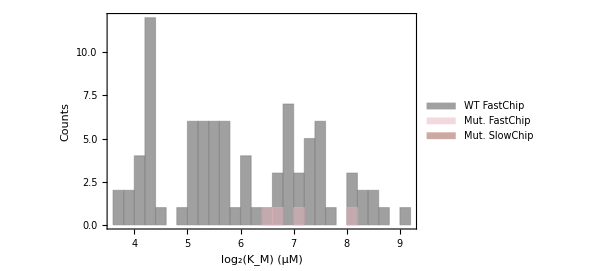
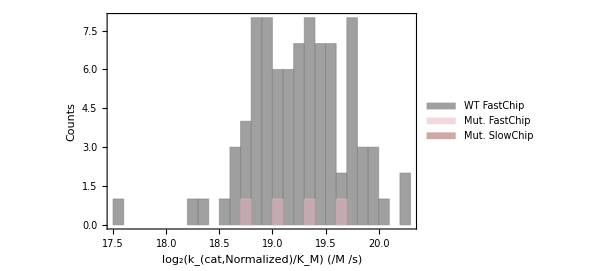
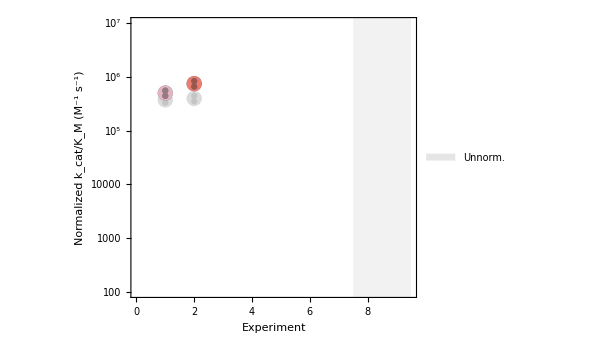
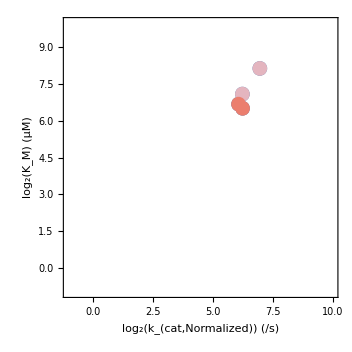
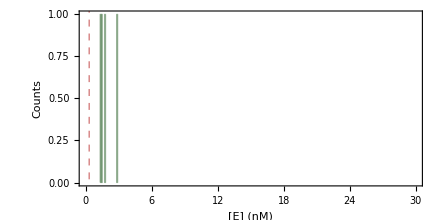
Mutation
-Graphics3D- | Aggregate Parameters
 | Median | StdDev | p-value | n_reps
k_cat (s^-1) | 75.8 | 26.3 | 0.14 | 4
K_M (μM) | 119.6 | 88.3 | 0.14 | 4
k_cat/K_M (M^-1 s^-1) | 606000 | 166000 | 0.98 | 4
Tier 1 |  |  |  | 
Total Chambers |  |  |  | 4
Expressed (>0.3nM) |  |  |  | 4
LLoD>5&&<6 2pt fits |  |  |  | 4
Tier 2 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A
Tier 3 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A | Michaelis-Menten curves
-Graphics-
-Graphics-
Michaelis-Menten fit parameters |  | 
 |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics-
Expression and Limit of Quantification |  | 
 |  | 
-Graphics-

 | -Graphics-
{}
{} | 
Experimental Data |  | 
Experiment | Chip Type | Plot Legend | Column | Row | [E] (nM) | k_(cat,Norm.) (/s) | K_M (μM) | K_M Limit | k_cat/K_(M,Norm.) | k_obs | p-value | R^2 | LBR
190117_S3_d1_MeP_1_GlyScan.csv | GlyScan | ● -Graphics- | 25 | 18 | 1.45 | 75.6 | 136.5 | 1 | 554000. | 486000. |  | 1. | 93.8
190117_S3_d1_MeP_1_GlyScan.csv | GlyScan | ○ -Graphics- | 28 | 42 | 1.34 | 125.1 | 282.6 | 1 | 443000. | 412000. |  | 1. | 60.
190123_S3_d1_MeP_1_GlyScan.csv | GlyScan | ● -Graphics- | 28 | 42 | 2.81 | 76. | 91.2 | 0 | 833000. | 777000. |  | 1. | 76.5
190123_S3_d1_MeP_1_GlyScan.csv | GlyScan | ○ -Graphics- | 25 | 18 | 1.78 | 67.6 | 102.7 | 1 | 658000. | 615000. |  | 1. | 87.3
Median k_cat |  |  |  |  |  | 75.8 |  |  |  |  | 0.14 |  | 
Median K_M |  |  |  |  |  |  | 119.6 |  |  |  | 0.14 |  | 
Median k_cat/K_M |  |  |  |  |  |  |  |  | 606000 | 550000 | 0.98 |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
Median WT k_cat |  |  |  |  |  | 34.2 |  |  |  |  |  |  | 
Median WT K_M |  |  |  |  |  |  | 48.9 | 1 |  |  |  |  | 
Median WT k_cat/K_M |  |  |  |  |  |  |  |  | 610000 | 502000 |  |  |  |  |

```mathematica
Print["Number of mutants with aggregate measurement:"]
Length[total]

datasetIn=Dataset[outForPDF];
(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_200923.wxf",datasetIn,PerformanceGoal->"Size"]*)

ds2=datasetIn[All,{"MutantID","Experiment","Indices","Column","Row","Data","EnzymeConc","AllSubstrateConcs","AllInitialRates","kcat","kcatNormalized","FitRSquared","BootstrapsFit","kcatCI","KmCI","kcatoverKMCI","kcatNormMean","kcatNormMedian","Km","KmLimit","KmMean","KmMedian","kcat/Km_Norm","kobs","kcat/Km_Norm_Mean","kcat/Km_Norm_Median","kcatNormBootstrapHypothesisTestMedian","KmBootstrapHypothesisTestMedian","kcat/Km_BootstrapHypothesisTestMedian","kcatNormBootstrapHypothesisTestMean","KmBootstrapHypothesisTestMean","kcat/Km_BootstrapHypothesisTestMean"}];

(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_noPlots.wxf",ds2,PerformanceGoal->"Size"]*)

keys=Keys[forCSV[[1]]]

out2=Prepend[Sort[Flatten[outForCSV,1],ToExpression[StringDrop[StringDrop[#1[[3]],-1],1]]<ToExpression[StringDrop[StringDrop[#2[[3]],-1],1]]&],keys];

(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_withlowR2.csv",out2,"Data"]*)

dataset=datasetIn[GroupBy["MutantID"]];

m=1;

(*If[m≤Length[total],Grid[{{dataset[m,1,"SummaryTableStructure"],dataset[m,1,"SummaryTableParams"],Column[{Style["Michaelis-Menten curves",Bold],dataset[m,1,"FitPlotNorm"],dataset[m,1,"KmNormPlot"]},Frame->All,Background->{LightGray,None}]},{Style["Michaelis-Menten fit parameters",Bold],SpanFromLeft},{},{dataset[m,1,"kcatNormHistogram"],dataset[m,1,"KmHistogram"],dataset[m,1,"kcat/Km_Histogram"]},{dataset[m,1,"ReplicatePlot"],dataset[m,1,"ReplicatePlotKm"],dataset[m,1,"kcatvsKmPlot"]},{Style["Expression and Limit of Quantification",Bold],SpanFromLeft},{},{dataset[m,1,"ExpressionHist"],dataset[m,1,"FractionCulledHist"]},{Style["Experimental Data",Bold],SpanFromLeft},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft}},Frame->True,Dividers->{{True,False,False,True,False,True,True,True},{True,True}},Background->{{None,None},{None,LightGray,None,None,None,LightGray,None,None,LightGray}},Alignment->Top,Spacings->2],Grid[{{Column[{dataset[m,1,"SummaryTableStructure"],Grid[{{Style["Expression",Bold]},{},{dataset[m,1,"ExpressionHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Column[{dataset[m,1,"SummaryTableParams"],Grid[{{Style["Limit of Quantification",Bold]},{},{dataset[m,1,"FractionCulledHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}]},{"",""}},Alignment->Top]]*)

If[m≤Length[total],Grid[{{dataset[m,1,"SummaryTableStructure"],dataset[m,1,"SummaryTableParams"],Column[{Style["Michaelis-Menten curves",Bold],dataset[m,1,"FitPlotNorm"],dataset[m,1,"KmNormPlot"]},Frame->All,Background->{LightGray,None}]},{Style["Michaelis-Menten fit parameters",Bold],SpanFromLeft},{},{dataset[m,1,"kcatNormHistogram"],dataset[m,1,"KmHistogram"],dataset[m,1,"kcat/Km_Histogram"]},{dataset[m,1,"ReplicatePlot"],"",dataset[m,1,"kcatvsKmPlot"]},{Style["Expression and Limit of Quantification",Bold],SpanFromLeft},{},{dataset[m,1,"ExpressionHist"],dataset[m,1,"FractionCulledHist"]},{Style["Experimental Data",Bold],SpanFromLeft},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft}},Frame->True,Dividers->{{True,False,False,True,False,True,True,True},{True,True}},Background->{{None,None},{None,LightGray,None,None,None,LightGray,None,None,LightGray}},Alignment->Top,Spacings->2],Grid[{{Column[{dataset[m,1,"SummaryTableStructure"],Grid[{{Style["Expression",Bold]},{},{dataset[m,1,"ExpressionHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Column[{dataset[m,1,"SummaryTableParams"],Grid[{{Style["Limit of Quantification",Bold]},{},{dataset[m,1,"FractionCulledHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}]},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft},{"",""}},Alignment->Top]]
```

```mathematica
maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

testF2[in_]:=Which[NumberQ[in],ToString[NumberForm[in,ScientificNotationThreshold->{-maxExponent,maxExponent}]],ListQ[in],ToString[NumberForm[#,ScientificNotationThreshold->{-maxExponent,maxExponent}]&/@in],NumberQ[in]==False&&ListQ[in]==False,in]
```

```mathematica
keys=Keys[forCSV[[1]]]

out2=Prepend[Sort[Flatten[outForCSV,1],ToExpression[StringDrop[StringDrop[#1[[3]],-1],1]]<ToExpression[StringDrop[StringDrop[#2[[3]],-1],1]]&],keys];

Export["~/Desktop/PafA_MeP_aggData_WTT79SNorm_v.2.0_200924.csv",Prepend[Map[testF2,Flatten[outForCSV,1],{2}],keys]]
```

{Version,RunDate,MutantID,Experiment,ChipType,Column,Row,EnzymeConc,AllSubstrateConcs,AllInitialRates,kcat,kcatNormalized,kcatLimit,KMFit,KMLimitValue,KMLimit,FitRSquared,kcatFitError,KMFitError,kcatoverKMFitError,kcatNormMean,kcatNormMedian,KMMean,KMMedian,kcat/KMNorm,kobsRaw,kobsNegCorrected,kcat/KMNormMean,kcat/KMNormMedian,kcatNormBootstrapHypothesisTestMedian,KMBootstrapHypothesisTestMedian,kcat/KMBootstrapHypothesisTestMedian,kobsBootstrapHypothesisTestMedian,Log2StdDevkcat,Log2StdDevKM,Log2StdDevkcat/KM,Log2StdDevkcat/KMLimit,kcatNormBootstrapHypothesisTestMean,KMBootstrapHypothesisTestMean,kcat/KMBootstrapHypothesisTestMean,kobsBootstrapHypothesisTestMean,NumCulledReps,LBR,FractionCulled,StdDevkcat,StdDevKM,StdDevkcat/KM,kcat/KMLimit,kcatAggLimit,KMAggLimit,kcat/KMAggLimit,KMMedianLimit,KMMeanLimit,kcat/KMNormMedianLimit,kcat/KMNormMeanLimit}

~/Desktop/PafA_MeP_aggData_WTT79SNorm_v.2.0_200923.csv